```mathematica
f=x^3-x y^2+y^3-y z^2+z^3;
xdot=x (-x+f);
ydot=y (x-y+f);
zdot=z (y-z+f);
vector={xdot,ydot,zdot};

a=1/Sqrt[14];

point={a,2 a,3 a};

transformedvector=TransformedField["Cartesian"->"Spherical",vector,{x,y,z}->{r,theta,phi}]/. r->1//Simplify
(*{0,1/4 Cos[theta] Sin[theta] (4 Cos[theta]+(-2 Cos[phi]-2 Cos[3 phi]-7 Sin[phi]+Sin[3 phi]) Sin[theta]),Cos[phi] (2 Cos[phi]-Sin[phi]) Sin[phi] Sin[theta]^2}*)
```

{0,1/4 Cos[theta] Sin[theta] (4 Cos[theta]+(-2 Cos[phi]-2 Cos[3 phi]-7 Sin[phi]+Sin[3 phi]) Sin[theta]),Cos[phi] (2 Cos[phi]-Sin[phi]) Sin[phi] Sin[theta]^2}

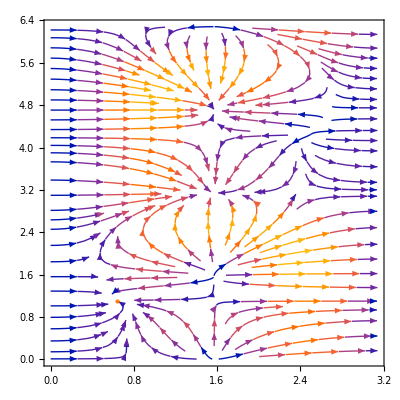

```mathematica
plot=StreamPlot[transformedvector//Rest//Evaluate,{theta,0,Pi},{phi,0,2 Pi}]~Show~Graphics@{Orange,PointSize@Large,Point@Rest@CoordinateTransform["Cartesian"->"Spherical",point]}
```

```mathematica
func={theta,phi}↦Evaluate@CoordinateTransform["Spherical"->"Cartesian",{1,theta,phi}]

plot3D=Graphics3D[(plot[[1]]/. (head:Arrow|Point)[z_]:>head[z/. {x_?NumericQ,y_}:>func@@{x,y}])]
```

Function[{theta,phi},{Cos[phi] Sin[theta],Sin[phi] Sin[theta],Cos[theta]}]

-Graphics3D-

```mathematica
plot3D~Show~Graphics3D@Ball[{0,0,0},0.98]
```

-Graphics3D-

```mathematica
eq={x[t] (-x[t]+x[t]^3-x[t] y[t]^2+y[t]^3-y[t] z[t]^2+z[t]^3),y[t] (x[t]+x[t]^3-y[t]-x[t] y[t]^2+y[t]^3-y[t] z[t]^2+z[t]^3),z[t] (x[t]^3+y[t]-x[t] y[t]^2+y[t]^3-z[t]-y[t] z[t]^2+z[t]^3)};

sol=ParametricNDSolveValue[{eq=={x'[t],y'[t],z'[t]},x[0]==Cos[b] Sin[c],y[0]==Sin[b] Sin[c],z[0]==Cos[c]},{x[t],y[t],z[t]},{t,0,20},{c,b}]

a=1/Sqrt[14.];Show[Graphics3D[{{Green,Ball[]},{Red,PointSize[.05],Point[{a,2 a,3 a}]}},Boxed->False],ParametricPlot3D[Evaluate[Table[sol[Pi/12,b],{b,0,2 Pi,.1}]],{t,0,10},PlotRange->All],ParametricPlot3D[Evaluate[Table[sol[Pi/3,b],{b,0,2 Pi,.1}]],{t,0,10},PlotRange->All]]
```

ParametricFunction[<>]

-Graphics3D-

```mathematica
eq1=eq/. {x[t]->a+e x1[t],y[t]->2 a+e y1[t],z[t]->3 a+e z1[t]};
s1=Series[eq1,{x1[t],0,1},{y1[t],0,1},{z1[t],0,1}];
eqL=s1//Normal;
eql=Series[eqL,{e,0,1}]//Normal;eqlp=Chop[eql/. e->1]

(*Out[]={-0.286351 x1[t]-0.0190901 y1[t]+0.286351 z1[t],0.496342 x1[t]-0.572703 y1[t]+0.572703 z1[t],-0.0572703 x1[t]+0.744513 y1[t]+0.0572703 z1[t]}*)
```

{-0.286351 x1[t]-0.0190901 y1[t]+0.286351 z1[t],0.496342 x1[t]-0.572703 y1[t]+0.572703 z1[t],-0.0572703 x1[t]+0.744513 y1[t]+0.0572703 z1[t]}

```mathematica
A=CoefficientArrays[eqlp,{x1[t],y1[t],z1[t]}]//Normal//Last

(*Out[]={{-0.286351,-0.0190901,0.286351},{0.496342,-0.572703,0.572703},{-0.0572703,0.744513,0.0572703}}*)
```

{{-0.286351,-0.0190901,0.286351},{0.496342,-0.572703,0.572703},{-0.0572703,0.744513,0.0572703}}

```mathematica
LyapunovSolve[Transpose[A],-{{1,0,0},{0,2,0},{0,0,3}}]//PositiveDefiniteMatrixQ

(*Out[]=False*)
```

False

```mathematica
Eigenvalues[A]
```

{-0.801784,-0.534522,0.534522}

```mathematica
sol=ParametricNDSolveValue[{eq=={x'[t],y'[t],z'[t]},x[0]==Cos[b] Sin[c],y[0]==Sin[b] Sin[c],z[0]==Cos[c]},{x[t],y[t],z[t]},{t,0,100},{c,b}];
Show[Graphics3D[{Green,Ball[]},Boxed->False],ParametricPlot3D[Evaluate[Table[sol[Pi/12,b],{b,.01,Pi/2,.02}]],{t,0,30},PlotRange->All],ParametricPlot3D[Evaluate[Table[sol[Pi/3,b],{b,0.01,Pi/2,.02}]],{t,0,30},PlotRange->All]]
{ParametricPlot3D[Evaluate[Table[sol[Pi/12,b],{b,.01,Pi/2,.01}]],{t,0,30},PlotRange->All,Boxed->False,AxesLabel->{x,y,z}],ParametricPlot3D[Evaluate[Table[sol[Pi/3,b],{b,0.01,Pi/2,.01}]],{t,0,30},PlotRange->All,Boxed->False,AxesLabel->{x,y,z}]}
```

ParametricNDSolveValue::ndsz: At t == 37.6212, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 34.194, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 30.943, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

-Graphics3D-

ParametricNDSolveValue::ndsz: At t == 35.1904, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 35.3623, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At t == 31.369, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

{-Graphics3D-,-Graphics3D-}

```mathematica
eq={x[t] (-x[t]+x[t]^3-x[t] y[t]^2+y[t]^3-y[t] z[t]^2+z[t]^3),y[t] (x[t]+x[t]^3-y[t]-x[t] y[t]^2+y[t]^3-y[t] z[t]^2+z[t]^3),z[t] (x[t]^3+y[t]-x[t] y[t]^2+y[t]^3-z[t]-y[t] z[t]^2+z[t]^3)};tm=23;sol=ParametricNDSolveValue[{eq=={x'[t],y'[t],z'[t]},x[0]==Cos[b] Sin[c],y[0]==Sin[b] Sin[c],z[0]==Cos[c]},{x[t],y[t],z[t]},{t,0,tm},{c,b}];
a=1/Sqrt[14];


Show[Graphics3D[{Green,Opacity[.4],Sphere[]},PlotRange->{{0,1},{0,1},{1/4,1}},Boxed->False],ParametricPlot3D[Evaluate[Table[sol[Pi/6,b],{b,.01,Pi/2,.02}]],{t,0,tm},PlotRange->All],ParametricPlot3D[Evaluate[Table[sol[Pi/3,b],{b,0.01,Pi/2,.02}]],{t,0,tm},PlotRange->All]]

Show[{ParametricPlot3D[Evaluate[Table[sol[Pi/6,b],{b,.01,Pi/2,.01}]],{t,0,tm},PlotRange->All,Boxed->False,AxesLabel->{x,y,z}],ParametricPlot3D[Evaluate[Table[sol[Pi/3,b],{b,0.01,Pi/2,.01}]],{t,0,tm},PlotRange->All,Boxed->False,AxesLabel->{x,y,z}]}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Alphabet[Entity["Language","Russian"]]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

```mathematica
Alphabet[Entity["Language","Chinese"]]
```

Alphabet::noalpha: The alphabet Chinese is not known or not available.

```mathematica
Alphabet[Entity["Language","Chinese"]]
```

Alphabet::noalpha: The alphabet Chinese is not known or not available.

Alphabet[Chinese]

```mathematica
Alphabet[Entity["Language","Greek"]]
```

```mathematica
{"α","β","γ","δ","ε","ζ","η","θ","ι","κ","λ","μ","ν","ξ","ο","π","ρ","σ","τ","υ","φ","χ","ψ","ω"}
```